### ρ^0→ π^++π^-

Es = 0.3879

ps = 0.361921

Mm1^2 = 0.0194798

ΔY = 0.387605

MTbar = 2.02234

ΔMT = 0.33993

mT^2Cosh[v*ΔY ]^2-pT^2 =0.145452

Root::npoly: {2.52603×10^110-3.551063780358×10^110 Cos[ζ]^4+4.40674×10^110 #1+(-7.46423×10^110+6.1335525949264×10^110 Cos[ζ]^4) #1^2-1.26999×10^111 #1^3+(1.00809×10^111-2.6485350420075×10^110 Cos[ζ]^4) #1^4+1.30054×10^111 #1^5-7.82756×10^110 #1^6-4.73238×10^110 #1^7+2.77793×10^110 #1^8,2.53767×10^110-«58» Cos[ζ]^4+«10»+2.79073×10^110 #1^8,«1»,«9»,«1»,«1»,«13»+1.55692×10^113 #1^8} is not a polynomial in #1.

General::stop: Further output of Root::npoly will be suppressed during this calculation.

Exact integral = 3.95947

Approx integral = 3.96102

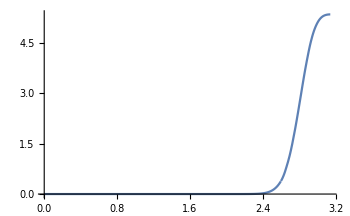
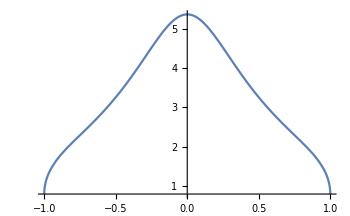
-Graphics3D- | -Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"];

eps=0.0;
(*parent / daughter info*)
M =0.77580;      m1 = 0.13957;     m2 = 0.13957;     W2 = m2^2;     Es=(M^2+m1^2-W2)/(2.M);     ps =√(Es^2-m1^2);     branch = 0.99;
Print["Es = ",Es];
Print["ps = ",ps];
Print["Mm1^2 = ",m1^2];
(*decayed pion's transverse momentum*)
pT = 0.9 ;    mT=√(m1^2+pT^2);
(* kinematic expressions for parent rapidity / MT ranges *)
ΔY = Log[(ps+√(Es^2+pT^2))/mT];     MTbar[v_]= (Es*mT*M*Cosh[v*ΔY])/(mT^2 Cosh[v*ΔY ]^2-pT^2);     ΔMT[v_]= (pT*M*√Abs[Es^2+pT^2-mT^2 Cosh[v*ΔY ]^2])/(mT^2 Cosh[v*ΔY ]^2-pT^2);
MT[v_,ζ_]= MTbar[v]+ΔMT[v]*Cos[ζ];
MTplot=Plot3D[MT[v,ζ],{v,-1,1},{ζ,0,Pi},ImageSize->350];
MTsliceplot=Plot[{MT[0,ζ],M},{ζ,0,Pi},ImageSize->350];

Print["ΔY = ", ΔY];
Print["MTbar = ", MTbar[-0.98156063424672]];
Print["ΔMT = ", ΔMT[-0.98156063424672]];
Print["mT^2Cosh[v*ΔY ]^2-pT^2 =",mT^2 Cosh[-0.98156063424672*ΔY ]^2-pT^2];

(* dN / dymTdmTdphiData *)
dNdypTdpTdphiData={{7.17752430*10^-03,1.26716073*10^+01},
{3.78993630*10^-02, 1.26703209*10^+01},
{9.35073360*10^-02, 1.26631844*10^+01},
{1.74611500*10^-01, 1.26382962*10^+01},
{2.82124830*10^-01, 1.25604265*10^+01},
{4.17333600*10^-01, 1.23251182*10^+01},
{5.81993540*10^-01, 1.17003753*10^+01},
{7.78479140*10^-01, 1.03909428*10^+01},
{1.01002170*10^+00, 8.31723044*10^+00},
{1.28110830*10^+00, 5.82371877*10^+00},
{1.59819070*10^+00, 3.49265839*10^+00},
{1.97106870*10^+00, 1.75925037*10^+00},
{2.41596300*10^+00, 7.22172273*10^-01},
{2.96389860*10^+00, 2.26919374*10^-01},
{3.69431420*10^+00, 4.59378348*10^-02}};

length=Length[dNdypTdpTdphiData[[1;;All,1]]];
dNdymTdmTdphiData=Table[{Sqrt[M^2+dNdypTdpTdphiData[[i,1]]^2],dNdypTdpTdphiData[[i,2]]},{i,1,length}];
dNdymTdmTdphiFunc=Interpolation[dNdymTdmTdphiData];

constant=5.04106;
slope=-2.13683;
leastsquarefit[MT_]=Exp[constant+slope*MT];
dNdymTdmTdphi[MT_]=Piecewise[{{dNdymTdmTdphiFunc[MT],M≤MT<2.96},{leastsquarefit[MT], MT ≥2.96}}];
LogPlot[dNdymTdmTdphi[MT],{MT,M,5}];
integrand[v_,ζ_]:=(M*branch*ΔY)/(4.Pi*ps)MT[v,ζ]/(√Abs[mT^2 Cosh[v*ΔY ]^2-pT^2])*dNdymTdmTdphi[MT[v,ζ]];
v0=0;ζ0=Pi;

plot3d=Plot3D[integrand[v,ζ],{v,-1,1},{ζ,0,Pi},PlotRange->All,ImageSize->350];
zetaslice=Plot[integrand[v0,ζ],{ζ,0,π},PlotRange->All,ImageSize->350];
vslice=Plot[integrand[v,ζ0],{v,-1,1},PlotRange->All,ImageSize->350];

GLpts={-0.98156063424672,-0.90411725637048,-0.76990267419431,-0.58731795428662,-0.3678314989982,-0.12523340851147,0.12523340851147,0.36783149899818,0.58731795428662,0.76990267419431,0.90411725637048,0.98156063424672};
GLweights={0.04717533638651,0.1069393259953,0.16007832854335,0.20316742672307,0.23349253653836,0.2491470458134,0.2491470458134,0.23349253653836,0.20316742672307,0.1600783285433,0.10693932599532,0.04717533638651};

Print["Exact integral = ",NIntegrate[integrand[v,ζ],{v,-1.0,1.0},{ζ,0.0,Pi},WorkingPrecision->6]];
Print["Approx integral = ",0.5*Pi*Sum[Sum[GLweights[[i]]*GLweights[[j]]*integrand[GLpts[[i]],0.5*Pi*(GLpts[[j]]+1.0)],{j,1,Length[GLpts]}],{i,1,Length[GLpts]}]];
Grid[{{plot3d,zetaslice,vslice}}]
```

#### Integral over v

```mathematica
ζ0=0.0;

vslice=Plot[integrand[v,ζ0],{v,-1,1},PlotRange->{0,integrand[0,ζ0]},ImageSize->350];

vIntExact=NIntegrate[integrand[v,ζ0],{v,-1,1}]

(*Test Gauss Legendre with 8 points; in general it's not symmetric in v because of the dN distribution, unless it's boost invariant*)

GLpts={-0.98156063424672,-0.90411725637048,-0.76990267419431,-0.58731795428662,-0.3678314989982,-0.12523340851147,0.12523340851147,0.36783149899818,0.58731795428662,0.76990267419431,0.90411725637048,0.98156063424672};

GLweights={0.04717533638651,0.1069393259953,0.16007832854335,0.20316742672307,0.23349253653836,0.2491470458134,0.2491470458134,0.23349253653836,0.20316742672307,0.1600783285433,0.10693932599532,0.04717533638651};

GCpts={-0.98078528040323,-0.83146961230255,-0.5555702330196,-0.19509032201613,0.19509032201613,0.5555702330196,0.8314696123025,0.98078528040323};
GCweights={0.076611790304042,0.21817192032594,0.3265173532116,0.38515347895797,0.385153478958,0.3265173532116,0.2181719203259,0.07661179030404};

GHpts={-2.9306374202572,-1.9816567566958,-1.1571937124468,-0.38118699020732,0.38118699020732,1.1571937124468,1.9816567566958,2.9306374202572};
GHweights={1.071930144248,0.866752606563,0.7928900483864,0.7645441286517,0.76454412865173,0.7928900483864,0.8667526065634,1.071930144248};

TRpts={-1.0,-0.8,-0.6,-0.4,-0.2,0.0,0.2,0.4,0.6,0.8,1.0};
TRweights={0.1,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.1};

vIntGaussLegendre=Sum[GLweights[[i]]*integrand[GLpts[[i]],ζ0],{i,1,Length[GLpts]}]
vIntGaussCheby=Sum[GCweights[[i]]*integrand[GCpts[[i]],ζ0],{i,1,Length[GCpts]}];
vIntGaussH=2/Pi Sum[(GHweights[[i]]*integrand[2/Pi ArcTan[GHpts[[i]]],ζ0])/(1.0+GHpts[[i]]^2),{i,1,Length[GHpts]}];
vIntTR=Sum[TRweights[[i]]*integrand[TRpts[[i]],ζ0],{i,1,Length[TRpts]}];
```

13.7554

13.7481

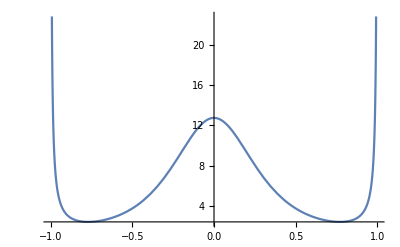

1+x^2

```mathematica
Plot[integrand[v,ζ0]*Sqrt[1-v^2],{v,-1,1}];
Plot[integrand[v,ζ0]*(1-v^2)^(-2/2),{v,-1,1}]

v=2/Pi ArcTan[x];

Sec[(Pi * v)/2]^2



Plot[integrand[2/Pi ArcTan[x],ζ0]*(Pi/2)/(1+x^2),{x,-10,10},PlotRange->All];
```

```mathematica
Clear[v]

2/(-1+(x-1)/(x+1))^2//Simplify

D[(1+v)/(1-v),v]//Simplify
```

1/2 (1+x)^2

2/(-1+v)^2

```mathematica
Plot[(2*(3*ΔY/2)integrand[(3*ΔY/2)((x-1)/(x+1)),ζ0])/(1+x)^2*Exp[x],{x,0,10},PlotRange->All];
```

#### Integral over ζ

```mathematica
v0=-0.0;

ζIntExact=NIntegrate[integrand[v0,ζ],{ζ,0,Pi}]

(*Test Gauss Legendre with 8 points; in general it's not symmetric in v because of the dN distribution, unless it's boost invariant*)

GLpts={-0.97822865814606,
-0.8870625997681,
-0.730152005574,
-0.51909612920681,
-0.26954315595235,
0,
0.26954315595235,
0.51909612920681,
0.73015200557405,
0.8870625997681,
0.97822865814606
};

GLweights={0.05566856711617,
0.12558036946491,
0.1862902109277,
0.23319376459199,
0.26280454451025,
0.2729250867779,
0.2628045445102,
0.233193764592,
0.1862902109277,
0.12558036946491,
0.055668567116174
};

TRpts={-1.0,-0.8,-0.6,-0.4,-0.2,0.0,0.2,0.4,0.6,0.8,1.0};
TRweights={0.1,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.1};

ζIntGaussLegendre=0.5*Pi * Sum[GLweights[[i]]*integrand[v0,0.5*Pi*(GLpts[[i]]+1.0)],{i,1,Length[GLpts]}]
ζIntGaussCheby=0.5*Pi*Sum[GCweights[[i]]*integrand[v0,0.5*Pi*(GCpts[[i]]+1.0)],{i,1,Length[GCpts]}];
ζIntTR=0.5*Pi *Sum[TRweights[[i]]*integrand[v0,0.5*Pi*(TRpts[[i]]+1)],{i,1,Length[TRpts]}]


0.5*Pi*NIntegrate[integrand[v0,0.5*Pi(x+1)],{x,-1,1}];

Plot[integrand[v0,0.5*Pi(x+1)],{x,-1,1}];
```

9.34969

9.35205

9.359

#### Fitting m_T slope of ideal ρ^0 dN/(dym_T dm_T dϕ_p) distribution

{0.775833,0.776725,0.781415,0.795207,0.825506,0.880927,0.969836,1.09904,1.27358,1.4977,1.77654,2.11825,2.53747,3.06375,3.77489}

0.0459378

0.0485459

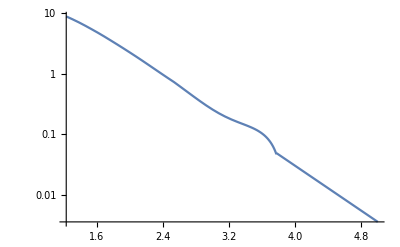

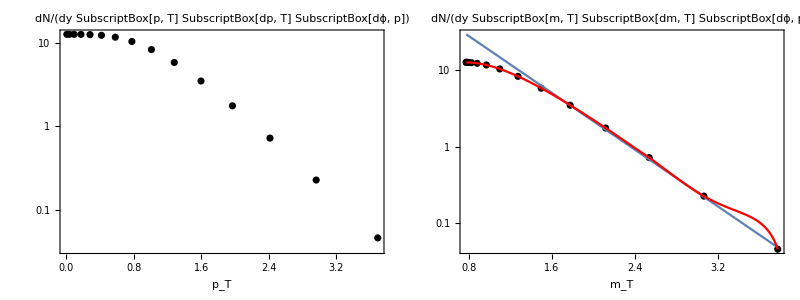

```mathematica
(*ideal thermal spectra of Subscript[ρ, 0] for 2+1d smooth central hydro*)

massRho =0.77580;

(*with flow*)
dNdypTdpTdphiData={{7.17752430*10^-03,1.26716073*10^+01},
{3.78993630*10^-02, 1.26703209*10^+01},
{9.35073360*10^-02, 1.26631844*10^+01},
{1.74611500*10^-01, 1.26382962*10^+01},
{2.82124830*10^-01, 1.25604265*10^+01},
{4.17333600*10^-01, 1.23251182*10^+01},
{5.81993540*10^-01, 1.17003753*10^+01},
{7.78479140*10^-01, 1.03909428*10^+01},
{1.01002170*10^+00, 8.31723044*10^+00},
{1.28110830*10^+00, 5.82371877*10^+00},
{1.59819070*10^+00, 3.49265839*10^+00},
{1.97106870*10^+00, 1.75925037*10^+00},
{2.41596300*10^+00, 7.22172273*10^-01},
{2.96389860*10^+00, 2.26919374*10^-01},
{3.69431420*10^+00, 4.59378348*10^-02}};

(*no flow*)
(*dNdypTdpTdphiData={{7.17752430*10^-03, 3.23249705*10^+01},
{3.78993630*10^-02, 3.21547904*10^+01},
{9.35073360*10^-02, 3.12744819*10^+01},
{1.74611500*10^-01, 2.88210705*10^+01},
{2.82124830*10^-01, 2.40791901*10^+01},
{4.17333600*10^-01, 1.73140145*10^+01},
{5.81993540*10^-01, 1.01734059*10^+01},
{7.78479140*10^-01, 4.67320673*10^+00},
{1.01002170*10^+00, 1.62045125*10^+00},
{1.28110830*10^+00, 4.11303390*10^-01},
{1.59819070*10^+00, 7.37147328*10^-02},
{1.97106870*10^+00, 8.83511050*10^-03},
{2.41596300*10^+00, 6.44173120*10^-04},
{2.96389860*10^+00, 2.36464242*10^-05},
{3.69431420*10^+00, 2.66140034*10^-07}};*)

length=Length[dNdypTdpTdphiData[[1;;All,1]]];

dNdymTdmTdphiData=Table[{Sqrt[massRho^2+dNdypTdpTdphiData[[i,1]]^2],dNdypTdpTdphiData[[i,2]]},{i,1,length}];

dNdymTdmTdphiData[[1;;All,1]]

mTmin=dNdymTdmTdphiData[[1,1]];
mTmax=dNdymTdmTdphiData[[15,1]];
dNmin=dNdymTdmTdphiData[[15,2]];
dNmax=dNdymTdmTdphiData[[1,2]];

dNdypTdpTdphiFunc=Interpolation[dNdypTdpTdphiData];
dNdymTdmTdphiFunc=Interpolation[dNdymTdmTdphiData];

constant=5.04106;
slope=-2.13683;

(*no flow fit *)
(*constant=8.4431;
slope=-6.23552;*)

leastsquarefit[mT_]:=Exp[constant+slope*mT];

dNdypTdpTdphiPlot=ListLogPlot[dNdypTdpTdphiData,Joined->False,Frame->True,FrameLabel->{Style["p_T",FontSize->16,FontFamily->"Arial",Black],""},PlotLabel->Style["dN/(dy SubscriptBox[p, T] SubscriptBox[dp, T] SubscriptBox[dϕ, p])",FontSize->20,FontFamily->"Arial",Black],PlotStyle->Black,ImageSize->400];

dNdymTdmTdphiPlot=Show[{{ListLogPlot[dNdymTdmTdphiData,Joined->False,Frame->True,PlotRange->{{mTmin,mTmax},{dNmin,leastsquarefit[mTmin]}},FrameLabel->{Style["m_T",FontSize->16,FontFamily->"Arial",Black],""},PlotLabel->Style["dN/(dy SubscriptBox[m, T] SubscriptBox[dm, T] SubscriptBox[dϕ, p])",FontSize->20,FontFamily->"Arial",Black],PlotStyle->Black,ImageSize->400],
LogPlot[leastsquarefit[mT],{mT,mTmin,mTmax},PlotRange->{{mTmin,mTmax},{dNmin,leastsquarefit[mTmin]}}],
LogPlot[dNdymTdmTdphiFunc[mT],{mT,mTmin,mTmax},Frame->True,PlotRange->{{mTmin,mTmax},{dNmin,leastsquarefit[mTmin]}},FrameLabel->{Style["m_T",FontSize->16,FontFamily->"Arial",Black],""},PlotLabel->Style["dN/(dy SubscriptBox[m, T] SubscriptBox[dm, T] SubscriptBox[dϕ, p])",FontSize->20,FontFamily->"Arial",Black],PlotStyle->Red,ImageSize->400]
}}];

dNdymTdmTdphi[MT_]:=Piecewise[{{dNdymTdmTdphiFunc[MT],mTmin≤MT<mTmax},{leastsquarefit[MT], MT ≥mTmax}}];

dNdymTdmTdphiData[[15,2]]
leastsquarefit[mTmax]

LogPlot[dNdymTdmTdphi[MT],{MT,massDelta,5}]

Grid[{{dNdypTdpTdphiPlot,dNdymTdmTdphiPlot}}]
```

#### Fitting m_T slope of ideal Δ^(++) dN/(dym_T dm_T dϕ_p) distribution

{1.23202,1.23258,1.23554,1.24431,1.26389,1.30077,1.36255,1.45734,1.5931,1.77738,2.01793,2.32442,2.71196,3.20975,3.89433}

{0.756399,0.75646,0.756777,0.7577,0.759626,0.762508,0.764095,0.756086,0.720722,0.636634,0.498097,0.330168,0.176966,0.0715965,0.0185203}

0.0185203

0.0192508

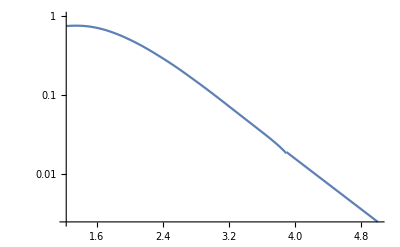

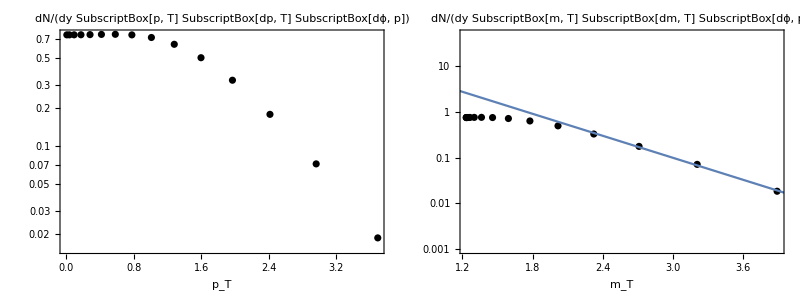

```mathematica
(*ideal thermal spectra of Subscript[ρ, 0] for 2+1d smooth central hydro*)

massDelta=1.23200;

(*with flow*)
dNdypTdpTdphiData={{7.17752430*10^-03, 7.56398936*10^-01},
{3.78993630*10^-02, 7.56459507*10^-01},
{9.35073360*10^-02, 7.56777102*10^-01},
{1.74611500*10^-01, 7.57699657*10^-01},
{2.82124830*10^-01, 7.59626386*10^-01},
{4.17333600*10^-01, 7.62507851*10^-01},
{5.81993540*10^-01, 7.64094901*10^-01},
{7.78479140*10^-01, 7.56085965*10^-01},
{1.01002170*10^+00, 7.20722428*10^-01},
{1.28110830*10^+00, 6.36634078*10^-01},
{1.59819070*10^+00, 4.98097282*10^-01},
{1.97106870*10^+00, 3.30168353*10^-01},
{2.41596300*10^+00, 1.76966426*10^-01},
{2.96389860*10^+00, 7.15965472*10^-02},
{3.69431420*10^+00, 1.85202569*10^-02}};

length=Length[dNdypTdpTdphiData[[1;;All,1]]];

dNdymTdmTdphiData=Table[{Sqrt[massDelta^2+dNdypTdpTdphiData[[i,1]]^2],dNdypTdpTdphiData[[i,2]]},{i,1,length}];

dNdymTdmTdphiData[[1;;All,1]]
dNdymTdmTdphiData[[1;;All,2]]

dNdypTdpTdphiFunc=Interpolation[dNdypTdpTdphiData];
dNdymTdmTdphiFunc=Interpolation[dNdymTdmTdphiData];

mTmin=Min[dNdymTdmTdphiData[[1;;All,1]]];
mTmax=Max[dNdymTdmTdphiData[[1;;All,1]]];
dNmin=Min[dNdymTdmTdphiData[[1;;All,2]]];
dNmax=Max[dNdymTdmTdphiData[[1;;All,2]]];

constant=3.22829;
slope=-1.84332;

leastsquarefit[mT_]:=Exp[constant+slope*mT];


dNdypTdpTdphiPlot=ListLogPlot[dNdypTdpTdphiData,Joined->False,Frame->True,FrameLabel->{Style["p_T",FontSize->16,FontFamily->"Arial",Black],""},PlotLabel->Style["dN/(dy SubscriptBox[p, T] SubscriptBox[dp, T] SubscriptBox[dϕ, p])",FontSize->20,FontFamily->"Arial",Black],PlotStyle->Black,ImageSize->400];

dNdymTdmTdphiPlot=Show[{{ListLogPlot[dNdymTdmTdphiData,Joined->False,Frame->True,PlotRange->{{massDelta,3.9},{0.001,50}},FrameLabel->{Style["m_T",FontSize->16,FontFamily->"Arial",Black],""},PlotLabel->Style["dN/(dy SubscriptBox[m, T] SubscriptBox[dm, T] SubscriptBox[dϕ, p])",FontSize->20,FontFamily->"Arial",Black],PlotStyle->Black,ImageSize->400],
LogPlot[leastsquarefit[mT],{mT,0,4},PlotRange->{{massDelta,3.9},{0.001,50}}]
}}];

dNdymTdmTdphi[MT_]:=Piecewise[{{dNdymTdmTdphiFunc[MT],mTmin≤MT<mTmax},{leastsquarefit[MT], MT ≥mTmax}}];

dNdymTdmTdphiFunc[mTmax]
leastsquarefit[mTmax]

LogPlot[dNdymTdmTdphi[MT],{MT,massDelta,5}]

Grid[{{dNdypTdpTdphiPlot,dNdymTdmTdphiPlot}}]
```

#### Fitting m_T slope of ideal Ω^2250 dN/(dym_T dm_T dϕ_p) distribution

{2.25201,2.25232,2.25394,2.25876,2.2696,2.29034,2.32599,2.38276,2.46813,2.5909,2.76147,2.99276,3.30278,3.72239,4.3266}

{0.000786109,0.000786178,0.000786541,0.000787622,0.000790062,0.000794746,0.000802807,0.000815452,0.000833115,0.000852814,0.000862408,0.000833991,0.000728211,0.00052466,0.000263493}

0.000263493

0.000263499

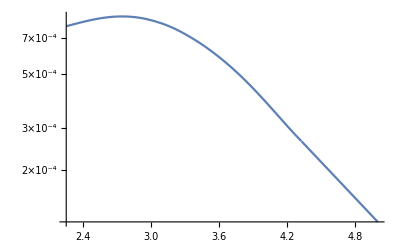

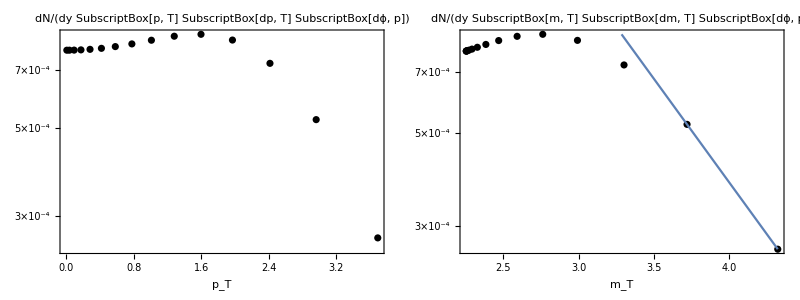

```mathematica
(*ideal thermal spectra of Subscript[ρ, 0] for 2+1d smooth central hydro*)

massOmega2250=2.252;

(*with flow*)
dNdypTdpTdphiData={{7.17752430*10^-03, 7.86109209*10^-04},
{3.78993630*10^-02, 7.86178059*10^-04},
{9.35073360*10^-02, 7.86541351*10^-04},
{1.74611500*10^-01, 7.87622313*10^-04},
{2.82124830*10^-01, 7.90061596*10^-04},
{4.17333600*10^-01, 7.94745544*10^-04},
{5.81993540*10^-01, 8.02807242*10^-04},
{7.78479140*10^-01, 8.15451790*10^-04},
{1.01002170*10^+00, 8.33115103*10^-04},
{1.28110830*10^+00, 8.52814350*10^-04},
{1.59819070*10^+00, 8.62408368*10^-04},
{1.97106870*10^+00, 8.33990877*10^-04},
{2.41596300*10^+00, 7.28211388*10^-04},
{2.96389860*10^+00, 5.24660067*10^-04},
{3.69431420*10^+00, 2.63493138*10^-04}};

length=Length[dNdypTdpTdphiData[[1;;All,1]]];

dNdymTdmTdphiData=Table[{Sqrt[massOmega2250^2+dNdypTdpTdphiData[[i,1]]^2],dNdypTdpTdphiData[[i,2]]},{i,1,length}];

dNdymTdmTdphiData[[1;;All,1]]
dNdymTdmTdphiData[[1;;All,2]]

dNdypTdpTdphiFunc=Interpolation[dNdypTdpTdphiData];
dNdymTdmTdphiFunc=Interpolation[dNdymTdmTdphiData];

mTmin=Min[dNdymTdmTdphiData[[1;;All,1]]];
mTmax=Max[dNdymTdmTdphiData[[1;;All,1]]];
dNmin=Min[dNdymTdmTdphiData[[1;;All,2]]];
dNmax=Max[dNdymTdmTdphiData[[1;;All,2]]];


constant=-3.3097;
slope=-1.13987;

leastsquarefit[mT_]:=Exp[constant+slope*mT];


dNdypTdpTdphiPlot=ListLogPlot[dNdypTdpTdphiData,Joined->False,Frame->True,FrameLabel->{Style["p_T",FontSize->16,FontFamily->"Arial",Black],""},PlotLabel->Style["dN/(dy SubscriptBox[p, T] SubscriptBox[dp, T] SubscriptBox[dϕ, p])",FontSize->20,FontFamily->"Arial",Black],PlotStyle->Black,ImageSize->400];

dNdymTdmTdphiPlot=Show[{{ListLogPlot[dNdymTdmTdphiData,Joined->False,Frame->True,PlotRange->{{mTmin,mTmax},{dNmin,dNmax}},FrameLabel->{Style["m_T",FontSize->16,FontFamily->"Arial",Black],""},PlotLabel->Style["dN/(dy SubscriptBox[m, T] SubscriptBox[dm, T] SubscriptBox[dϕ, p])",FontSize->20,FontFamily->"Arial",Black],PlotStyle->Black,ImageSize->400],
LogPlot[leastsquarefit[mT],{mT,mTmin,mTmax},PlotRange->{{mTmin,mTmax},{dNmin,dNmax}}]
}}];

dNdymTdmTdphi[MT_]:=Piecewise[{{dNdymTdmTdphiFunc[MT],mTmin≤MT<mTmax},{leastsquarefit[MT], MT ≥mTmax}}];

dNdymTdmTdphiFunc[mTmax]
leastsquarefit[mTmax]

LogPlot[dNdymTdmTdphi[MT],{MT,mTmin,5}]

Grid[{{dNdypTdpTdphiPlot,dNdymTdmTdphiPlot}}]
```